```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,100,200,300,400,450,500,530};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>"data.dat"],{i,1,Length[mub]}];
```

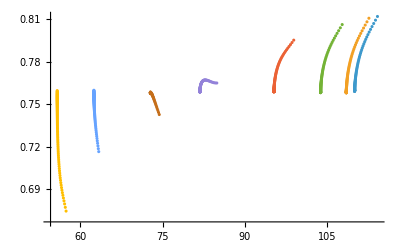

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.759)/0.759]==0.01,{x,fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p01.dat",%];
```

InterpolatingFunction::dmval: 输入值 {114.2} 位于插值函数的数据范围之外. 将使用外推法.

FindRoot::reged: 点 {110.019} 位于搜索区域 {110.019,114.2} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

InterpolatingFunction::dmval: 输入值 {112.639} 位于插值函数的数据范围之外. 将使用外推法.

FindRoot::reged: 点 {108.515} 位于搜索区域 {108.515,112.639} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

InterpolatingFunction::dmval: 输入值 {107.762} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

FindRoot::reged: 点 {103.817} 位于搜索区域 {103.817,107.762} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{110.019,108.515,103.817,95.2972,84.8777,73.5964,62.4473,55.7501}

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.759)/0.759]==0.02,{x,fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p02.dat",%];
```

InterpolatingFunction::dmval: 输入值 {114.2} 位于插值函数的数据范围之外. 将使用外推法.

FindRoot::reged: 点 {110.019} 位于搜索区域 {110.019,114.2} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

InterpolatingFunction::dmval: 输入值 {112.639} 位于插值函数的数据范围之外. 将使用外推法.

FindRoot::reged: 点 {108.515} 位于搜索区域 {108.515,112.639} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

InterpolatingFunction::dmval: 输入值 {107.762} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

FindRoot::reged: 点 {103.817} 位于搜索区域 {103.817,107.762} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{110.019,108.515,103.817,95.2972,84.8777,74.2746,62.4473,55.7501}

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.759)/0.759]==0.03,{x,fitdata[[i]][[-1]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p03.dat",%];
```

InterpolatingFunction::dmval: 输入值 {114.2} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {112.639} 位于插值函数的数据范围之外. 将使用外推法.

InterpolatingFunction::dmval: 输入值 {107.762} 位于插值函数的数据范围之外. 将使用外推法.

General::stop: 在本次计算中，InterpolatingFunction::dmval 的进一步输出将被抑制.

FindRoot::reged: 点 {84.8777} 位于搜索区域 {81.7705,84.8777} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {74.3777} 位于搜索区域 {72.7665,74.3777} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {55.7501} 位于搜索区域 {55.7501,57.3672} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{110.804,109.318,104.697,96.5423,84.8777,74.3777,62.7183,55.7501}

```mathematica
Export["mub.dat",mub]
```

mub.dat

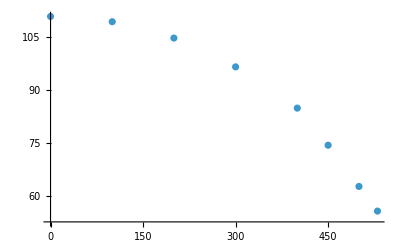

```mathematica
ListPlot[Transpose[{mub,T}],PlotRange->All]
```